## Integer Addition with Variable-Length Output

This example demonstrates how to train nets on sequences where both the input and output are variable-length sequences, and those sequences are not the same.

One sophisticated example of this task is translating English to German, but the example we cover is a simpler problem

Taking a string that describes a sum, e.g. 250 plus 123, and producing an output string that describes the answer, for instance 373.

The method used is based on I. Sutskever et al., Sequence to Sequence Learning with Neural Networks, 2014

Create training data based on strings that describe three-digit additions and the corresponding result as a string

```mathematica
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->IntegerString[a+b];
data=RandomSample[Flatten@Table[makeRule[i,j],{i,0,999},{j,0,999}],60000];
{testData,trainingData}=TakeDrop[data,6000];
```

```mathematica
RandomSample[trainingData,4]//InputForm
```

{"281+126" -> "407", "768+618" -> "1386", 
 "371+171" -> "542", "588+531" -> "1119"}

Create a NetEncoder that uses a special code for the start and end of a string, which will be used to indicate the beginning and end of the output sequence

```mathematica
targetEnc=NetEncoder[{"Characters",{DigitCharacter,{StartOfString,EndOfString}->Automatic}}]
```

NetEncoder[<>]

Evaluate the encoder on an input string

```mathematica
targetEnc["1"]
```

{11,2,11}

Create a similar encoder for the input, which contains a plus

```mathematica
inputEnc=NetEncoder[{"Characters",{DigitCharacter,"+"}}]
```

NetEncoder[<>]

Define a net that takes a sequence of inputs and returns a single vector of size 150 as output:

```mathematica
encoderNet=NetChain[{UnitVectorLayer[],GatedRecurrentLayer[150],SequenceLastLayer[]}]
```

NetChain[<>]

Define a net that takes an input vector of size 150 and a sequence of vectors as input and returns a sequence of vectors as output:

```mathematica
decoderNet=NetGraph[{
UnitVectorLayer[11],
SequenceMostLayer[],
GatedRecurrentLayer[150],
NetMapOperator[LinearLayer[]],
SoftmaxLayer[]},
{NetPort["Input"]->1->2->3->4->5,
NetPort["State"]->NetPort[3,"State"]}
]
```

NetGraph[<>]

Define a net with a CrossEntropy Layer and containing the encoder and decoder nets

```mathematica
trainingNet=NetGraph[<|"encoder"->encoderNet,"decoder"->decoderNet,"loss"->CrossEntropyLossLayer["Index"],"rest"->SequenceRestLayer[]|>,
{NetPort["Input"]->"encoder"->NetPort["decoder","State"],
NetPort["Target"]->NetPort["decoder","Input"],
"decoder"->NetPort["loss","Input"],
NetPort["Target"]->"rest"->NetPort["loss","Target"]},
"Input"->inputEnc,"Target"->targetEnc]
```

NetGraph[<>]

Train the net (this procedure is often referred to as teacher forcing)

```mathematica
trainedNet=NetTrain[trainingNet,trainingData,ValidationSet->testData,MaxTrainingRounds->30,TargetDevice->"GPU"]
```

NetGraph[<>]

In this case of three-digit addition, there are only 1999 possible outputs.

It is feasible to calculate the loss for each output and find the one that minimizes the loss

```mathematica
predict[input_]:=First@Ordering[trainedNet[<|"Input"->ConstantArray[input,1999],"Target"->Table[ToString[i],{i,1999}]|>],1]
```

Predict the output, given a number of inputs and the trained net:

```mathematica
predict/@{"34+200","32+87","344+77"}
```

{233,116,420}

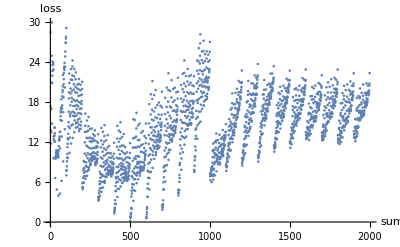

```mathematica
input="200+300";
ListPlot[trainedNet[<|"Input"->ConstantArray[input,1999],"Target"->Table[IntegerString[i],{i,1999}]|>],AxesLabel->{"sum","loss"}]
```

A more efficient way of obtaining predictions is to generate the output until the End of String virtual character is reached

First, extract the trained encoder and decoder subnets from the trained NetGraph, and attach appropriate encoders and decoders

```mathematica
trainedEncoder=NetReplacePart[NetExtract[trainedNet,"encoder"],"Input"->inputEnc]
```

NetChain[<>]

```mathematica
trainedDecoder=NetExtract[trainedNet,"decoder"]
```

NetGraph[<>]

Use a sequence last layer to make a version of the decoder that only produces predictions for the last character of the answer, given the previous characters.

Here a character decoder is attached for the probability vector using the same alphabet as the Target input

```mathematica
charPredictor1=NetGraph[{trainedDecoder,SequenceLastLayer[]},{1->2},"Input"->targetEnc,"Output"->NetDecoder[targetEnc]]
```

NetGraph[<>]

Apply the decoder to a partial answer

```mathematica
state=trainedEncoder["25+25"];
charPredictor1[<|"Input"->"5","State"->state|>]//InputForm
```

"0"

When the decoder predicts the end of the target string, an empty string will be produced:

```mathematica
charPredictor1[<|"Input"->"50","State"->state|>]//InputForm
```

""

Now define a prediction function that takes the encoder and decoder nets and an input string. The function will compute successively longer results until the decoder claims to be finished:

```mathematica
predict2[input_]:=Module[
{encoded=trainedEncoder[input],result="",prediction},
Do[
prediction=charPredictor1[<|"Input"->result,"State"->encoded|>];
If[prediction==="",Break[]];
result=result<>prediction,
100]; (* stop at length 100, just in case *)
result
]
```

Evaluate this prediction function on input data:

```mathematica
predict2["564+200"]//InputForm
```

"763"

```mathematica
inputs={"564+200","44+87","344+67"};
predict2/@inputs
```

{763,132,411}

This is an good approximation to the first method, which finds the exact maximum likelihood answer:

```mathematica
predict/@inputs
```

{763,132,411}

The naive technique of generating by passing in each partial answer to the decoder net to derive the next character has time complexity of n squared, where n is the length of the output sequence, and so is not appropriate for generating longer sequences.

Net State Object can be used to generate with time complexity of n.

First, a decoder is created that takes a single character and predicts the next character.

The recurrent state of the Gated Recurrent Layer is handled by a net state object at a later point.

Obtain the trained gated recurrent layer and linear layer from the trained net.

```mathematica
gru=NetExtract[trainedNet,{"decoder",3}]
linear=NetExtract[trainedNet,{"decoder",4,"Net"}]
```

GatedRecurrentLayer[<>]

LinearLayer[<>]

Define a class encoder and decoder that will encode and decode individual characters, as well as the special classes to indicate the start and end of the string.

```mathematica
digits=Characters["0123456789"];
classEnc=NetEncoder[{"Class",Append[digits,StartOfString]}];
classDec=NetDecoder[{"Class",Append[digits,EndOfString]}];
```

Define a net that takes a single character, runs one step of the Gated Recurrent Layer, and produces a single softmax prediction.

```mathematica
charPredictor2=NetChain[{UnitVectorLayer[],ReshapeLayer[{1,11}],gru,ReshapeLayer[{150}],linear,SoftmaxLayer[]},"Input"->classEnc,"Output"->classDec]
```

NetChain[<>]

This predictor has an internal recurrent state, as revealed by NetInformation

```mathematica
NetInformation[charPredictor2,"RecurrentStatesPositionList"]
```

{{3,State}}

Create a function that uses Net STate Object to memorize the internal recurrent state, which is seeded from the code produced by the trained encoder:

```mathematica
predict3[input_]:=Module[{code,sobj,res},
code=trainedEncoder[input];
sobj=NetStateObject[charPredictor2,<|{3,"State"}->code|>];
res=NestWhileList[sobj,StartOfString,#=!=EndOfString&];
StringJoin@res[[2;;-2]]
]
```

Apply the function to some inputs to obtain predicted sequences:

```mathematica
predict3["111+111"]//FullForm
```

"222"

```mathematica
predict3/@{"564+200","44+87","344+67"}
```

{763,132,411}

Obtain the accuracy of the trained net on the test set:

```mathematica
prediction=predict3/@Keys[testData];
accuracy=N@Mean@Boole@MapThread[Equal,{prediction,Values[testData]}]
```

0.493667